```mathematica
p=({{1, 3}, {-2, 2}});
```

```mathematica
p^2//MatrixForm
```

(1 | 9
4 | 4)

```mathematica
p=({{3, -2, 1}, {-2, 1, 0}, {1, 0, 4}});
```

```mathematica
Det[p]
```

-5

```mathematica
CharacteristicPolynomial[p,x]
```

-5-14 x+8 x^2-x^3

```mathematica
N[Eigenvalues[p],10]
```

{5.,3.302775638,-0.3027756377}

```mathematica
Eigenvectors[p]//N
```

{{2.,-1.,2.},{-0.697224,0.605551,1.},{-4.30278,-6.60555,1.}}

```mathematica
Eigensystem[p]
```

{{5,1/2 (3+√13),1/2 (3-√13)},{{2,-1,2},{1/2 (-5+√13),-3+√13,1},{1/2 (-5-√13),-3-√13,1}}}

```mathematica
Options[Plot]
```

```mathematica
{AlignmentPoint->Center,AspectRatio->1/GoldenRatio,Axes->True,AxesLabel->None,AxesOrigin->Automatic,AxesStyle->{},Background->None,BaselinePosition->Automatic,BaseStyle->{},ClippingStyle->None,ColorFunction->Automatic,ColorFunctionScaling->True,ColorOutput->Automatic,ContentSelectable->Automatic,CoordinatesToolOptions->Automatic,DisplayFunction:>$DisplayFunction,Epilog->{},Evaluated->Automatic,EvaluationMonitor->None,Exclusions->Automatic,ExclusionsStyle->None,Filling->None,FillingStyle->Automatic,FormatType:>TraditionalForm,Frame->False,FrameLabel->None,FrameStyle->{},FrameTicks->Automatic,FrameTicksStyle->{},GridLines->None,GridLinesStyle->{},ImageMargins->0.,ImagePadding->All,ImageSize->Automatic,ImageSizeRaw->Automatic,LabelingSize->Automatic,LabelStyle->{},MaxRecursion->Automatic,Mesh->None,MeshFunctions->{#1&},MeshShading->None,MeshStyle->Automatic,Method->Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel->None,PlotLabels->None,PlotLegends->None,PlotPoints->Automatic,PlotRange->{Full,Automatic},PlotRangeClipping->True,PlotRangePadding->Automatic,PlotRegion->Automatic,PlotStyle->Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions->Automatic,Prolog->{},RegionFunction->(True&),RotateLabel->True,ScalingFunctions->None,TargetUnits->Automatic,Ticks->Automatic,TicksStyle->{},WorkingPrecision->MachinePrecision}
```

```mathematica
Graphics[{{Text[A,{-1,1.1}],Red,PointSize[0.03],Point[{-1,1}]},
Text[B,{1,0.9}],Blue,PointSize[Large],Point[{1,1}],
{Magenta,Thick,HalfLine[{0,0},{1,0}]},
{Green,Thick,Dashed,InfiniteLine[{0,0},{-1,1}]}},PlotRange->{{-1.2,1.2},{-0.2,1.5}},Frame->True]
```

-Graphics-

```mathematica
pa=Graphics[{Text[A,{-1,1.1}],Red,PointSize[0.03],Point[{-1,1}]}];
pb=Graphics[{Text[B,{1,0.9}],Blue,PointSize[Large],Point[{1,1}]}];
hl=Graphics[{Magenta,Thick,HalfLine[{0,0},{1,0}]}];
il=Graphics[{Green,Thick,Dashed,InfiniteLine[{0,0},{-1,1}]}];
Show[{pa,pb,hl,il},PlotRange->{{-1.2,1.2},{-0.2,1.5}},Frame->True]
```

-Graphics-

```mathematica
pa=Graphics[{Text[A,{-1,1.1}],Red,PointSize[0.03],Point[{-1,1}]}];
pb=Graphics[{Text[B,{1,0.9}],Blue,PointSize[Large],Point[{1,1}]}];
hl=Graphics[{Magenta,Thick,HalfLine[{0,0},{1,0}]}];
il=Graphics[{Green,Thick,Dashed,InfiniteLine[{0,0},{-1,1}]}];
Show[{pa,pb,hl,il},PlotRange->{{-1.2,1.2},{-0.2,1.5}},Frame->True]
```

-Graphics-

```mathematica
Δ=Triangle[{{0,0},{1,1},{2,-1}}];
Graphics[{RGBColor[0.3,1,0.7].Δ}];
Graphics[{EdgeForm[Thick],Pink,Rotate[Δ,Degree 60]}]
```

-Graphics-

```mathematica
Graphics3D[Triangle[{{0,0,1},{1,1,2},{2,-1,3}}]]
```

-Graphics3D-

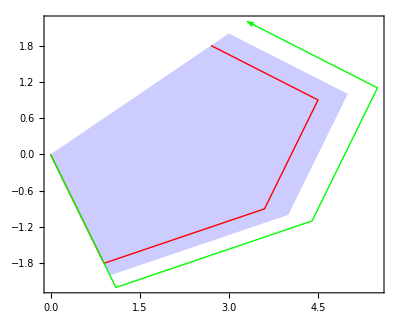

```mathematica
pts={{0,0},{1,-2},{4,-1},{5,1},{3,2}};
g1=Graphics[{Opacity[0.2],Blue,Polygon[pts]}];
g2=Graphics[{Red,Line[0.9pts]}];
g3=Graphics[{Green,Arrow[1.1pts]}];
Show[{g1,g2,g3},Frame->True]
```

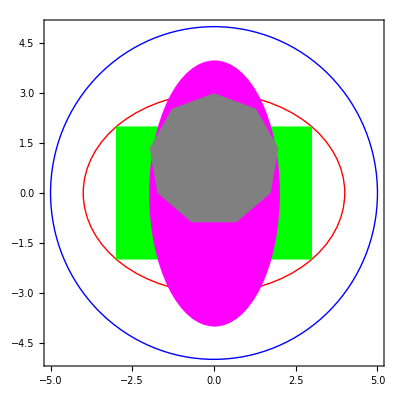

```mathematica
(* 2D графични обекти *)
g1=Graphics[{Blue,Circle[{0,0},5]}];
g2=Graphics[{Red,Circle[{0,0},{4,3}]}];
g3=Graphics[{Green,Rectangle[{-3,-2},{3,2}]}];
g4=Graphics[{Magenta,Disk[{0,0},{2,4}]}];
g5=Graphics[{Gray,RegularPolygon[{0,1},2,9]}];
Show[{g1,g2,g3,g4,g5},Frame->True,ContentSelectable->True]
```

```mathematica
h1=Graphics[{Blue,DiskSegment[{0,0},5,{Pi/6,3 Pi/4}]}];
h2=Graphics[{Orange,Disk[{0,0},4,{-Pi/6,-3 Pi/4}]}];
h3=Graphics[{Yellow,Translate[SSSTriangle[4,5,7],{-3,1}]}];
h4=Graphics[{Red,Translate[SASTriangle[5,Degree 50,2],{-2,-2}]}];
h5=Graphics[ListPlot[CirclePoints[2,9],PlotStyle->PointSize[0.03]]];
Show[h1,h2,h3,h4,h5,Frame->True]
```

-Graphics-

```mathematica
(* 3D графични обекти *)
b1=Graphics3D[Cuboid[{0,0,0}]];
b2=Graphics3D[Parallelepiped[{-2,-3,-2},{{1,0,0},{0,1,1},{1,1,0}}]];
b3=Graphics3D[Tetrahedron[{{2,-1,3},{-1,0,0},{0,-1,0},{0,0,-1}}]];
Show[{b1,b2,b3},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
b4=Graphics3D[Cone[{{0,0,0},{2,2,2}},1]];
b5=Graphics3D[Ball[{1,1,1}],1];
b6=Graphics3D[Tetrahedron[{{2,1,3},{-1,0,0},{0,-1,0},{0,0,-1}}]];
Show[{b4,b5,b6},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
b7=Graphics3D[{Opacity[0.4],Cylinder[{{0,0,0},{5,2,3}},2]}];
b8=Graphics3D[Opacity[0.2],Ellipsoid[{1,1,1},{2,3,4}]];
b9=Graphics3D[{Prism[{{5,0,3},{0,0,0},{3,0,0},{5,5,3},{0,5,0},{3,5,0}}]}];
Show[{b7,b8,b9},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
a={{-1,0},{3,0},{0,4}};
Graphics[Rotate[{Red,Circumsphere[a],Blue,Triangle[a]},Pi/3],Frame->True]
```

-Graphics-

```mathematica
(* Дефиниране и изобразяване на области *)
Ω=ImplicitRegion[x^2/9+y^2/4≤1,{x,y}];
RegionPlot[Ω,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Ω=ImplicitRegion[x^2/9+y^2/4≤1&&x^2+y^2≥1&&2 x-y≤3,{x,y}];
RegionPlot[Ω,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Ω=ImplicitRegion[{-3 x+4 y+z≤12,5 x-2 y-z≤8,x+y+2 z≤4,2 x+4 y≥2,x≥0,y≥0,z≥0},{x,y,z}];
RegionPlot3D[Ω,Axes->True]
```

-Graphics3D-

```mathematica
Graphics[{{Blue,Annulus[{0,0},{1,3}]},{Opacity[0.7],Brown,StadiumShape[{{-1,2},{2,3}},2]}},Frame->True]
```

-Graphics-

```mathematica
Graphics[{{Opacity[0.7],Brown,StadiumShape[{{-1,2},{2,3}},2]},{Blue,Annulus[{0,0},{1,3}]}},Frame->True]
```

-Graphics-

```mathematica
Ω=Tube[{{-1,-1,-1},{0,0,1},{1,1,-1}},0.4];
{Graphics3D[{Red,Ω}],Graphics3D[{Green,CapForm["Round"],Ω}],Graphics3D[{JoinForm["Miter"],Ω}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Graphics3D[CapsuleShape[{{-2,0,0},{0,0,3}},1],Axes->True]
```

-Graphics3D-

```mathematica
a={{-1,0},{3,0},{0,4}};
Graphics[Rotate[{Thick,Red,Circumsphere[a],Lighter[Blue],Triangle[a]},Pi/3],Frame->True]
```

-Graphics-

```mathematica
a={{-1,0},{3,0},{0,4}};
Graphics[Rotate[{Cyan,Triangle[a],Red,Thick,Insphere[a]},Pi/3],Frame->True]
```

-Graphics-

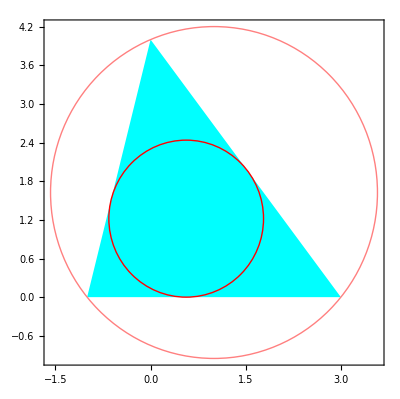

```mathematica
a={{-1,0},{3,0},{0,4}};
g1=Graphics[{Cyan,Triangle[a]}];
g2=Graphics[{Red,Thick,Insphere[a]}];
g3=Graphics[{Pink,Thick,Circumsphere[a]}];
Show[{g1,g2,g3},Frame->True]
```

```mathematica
a={{-1,0},{3,0},{0,4}};
s1={EdgeForm[Thick],Cyan,Triangle[a]};
s2={Red,Thick,Insphere[a]};
s3={Pink,Thick,Circumsphere[a]};
Show[Graphics[Rotate[{s1,s2,s3},Degree 45]],Frame->True]
```

-Graphics-

```mathematica
b={{-1,0,1},{3,2,2},{0,4,-3},{5,-2,-1}};
s1={Opacity[0.4],EdgeForm[Thick],Cyan,Tetrahedron[b]};
s2={Red,Thick,Insphere[b]};
s3={Opacity[0.2],Pink,Thick,Circumsphere[b]};
Show[Graphics3D[{s1,s2,s3}],Axes->True]
```

-Graphics3D-

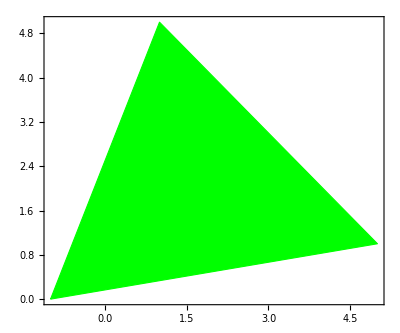

4 √2+√37

14

{5/3,2}

```mathematica
(* Числови характеристики на геометрични обекти *)
a={{-1,0},{5,1},{1,5}};
Graphics[{Green,EdgeForm[Thick],Polygon[a]},Frame->True]
ArcLength[Line[a]]
Area[Triangle[a]]
RegionCentroid[Triangle[a]]
```

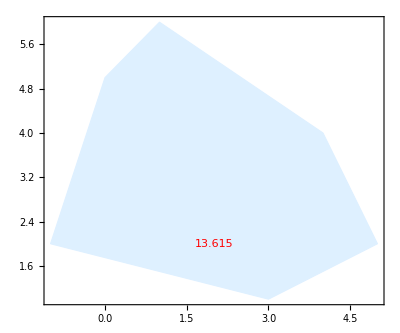

```mathematica
b={{-1,2},{3,1},{5,2},{4,4},{1,6},{0,5}};
Graphics[{LightBlue,EdgeForm[Thick],Polygon[b],Red,Text[N[ArcLength[Line[b]]],{2,2}]},Frame->True]
```

```mathematica
ArcLength[Line[b]]
```

√2+2 √5+√13+√17

```mathematica
Area[Polygon[b]]
```

18

```mathematica
RegionCentroid[Polygon[b]]
```

{101/54,86/27}

```mathematica
ArcLength[{1-5 t,3 t^2-2},{t,0,2}]
```

13+25/12 ArcSinh[12/5]

```mathematica
f[x_]:=x^3-2 x Cos[x]
ArcLength[{x,f[x]},{x,0,2}]
```

∫_0^2 √(1+(3 x^2-2 Cos[x]+2 x Sin[x])^2)ⅆx

```mathematica
ArcLength[{3Cos[θ],2Sin[θ]},{θ,0,2 Pi}]
```

8 EllipticE[-5/4]

```mathematica
a=2;
ArcLength[{a(Cos[θ])^3,a(Sin[θ])^3},{θ,0,2 Pi}]
```

12

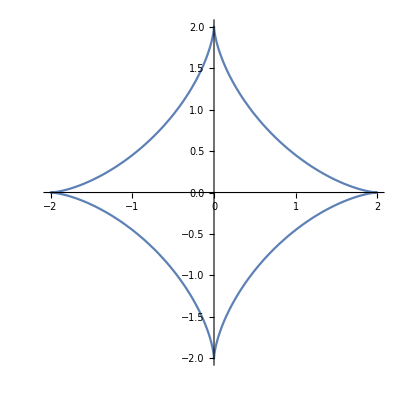

```mathematica
ParametricPlot[{a(Cos[θ])^3,a(Sin[θ])^3},{θ,0,2 Pi}]
```

```mathematica
Ω=ImplicitRegion[x^2/9+y^2/4≤1&&x^2+y^2≥1&&2 x-y≤3,{x,y}];
Area[Ω]//N
```

11.754

```mathematica
RegionCentroid[Ω]//N
```

{-0.6608,0.146845}

```mathematica
g1=RegionPlot[Ω];
g2=Graphics[{Red,PointSize[0.02],Point[RegionCentroid[Ω]]}];
Show[{g1,g2},AspectRatio->Automatic]
```

-Graphics-

```mathematica
f[x_]:=x^3-2 x Cos[x]
ArcLength[{x,f[x]},{x,0,2},Method->"NIntegrate",WorkingPrecision->30]
```

11.6570914434164332738605536292

```mathematica
Ω=Tetrahedron[{{-1,0,1},{3,2,2},{0,4,-3},{5,-2,-1}}];
Volume[Ω]
```

67/3

```mathematica
RegionCentroid[Ω]
```

{7/4,1,-1/4}

```mathematica
RegionDistance[Ω,{5,6,7}]
```

3 √5

```mathematica
RegionNearest[Ω,{5,6,7}]
```

{3,2,2}

```mathematica
(*Ω=ImplicitRegion[x^2/9+y^2/4+z^2/9≤1&&x^2+y^2+z^2≥1&&2 x-y-z≤3,{x,y,z}];
Volume[Ω,Method->"NIntegrate"]
RegionCentroid[Ω]*)
```

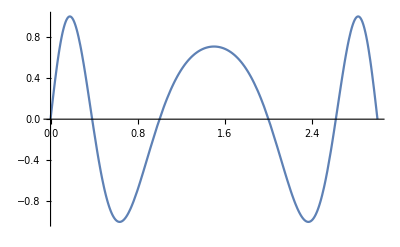

```mathematica
(* Графики и криви в рвнината *)
f[x_]:=Sin[π x(3-x)]
Plot[f[x],{x,0,3}]
```

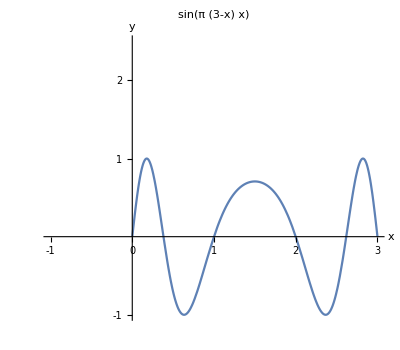

```mathematica
f[x_]:=Sin[π x(3-x)]
Plot[f[x],{x,0,3},Ticks->{{-1,0,1,2,3},{-1,1,2}},AxesLabel->{x,y},
AspectRatio->Automatic,PlotRange->{{-1,3},{-1,2.5}},PlotLabel->f[x]]
```

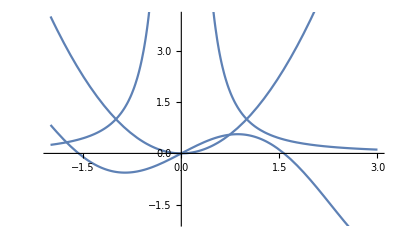

```mathematica
a=-2;
b=3;
gr1=Plot[x^2,{x,a,b}];
gr2=Plot[1/x^2,{x,a,b}];
gr3=Plot[x Cos[x],{x,a,b}];
Show[{gr1,gr2,gr3},PlotRange->{-2,4}]
```

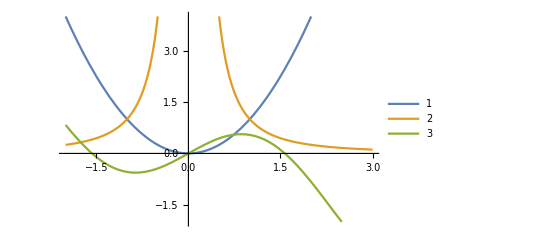

```mathematica
Plot[{x^2,1/x^2,x Cos[x]},{x,-2,3},PlotRange->{-2,4},PlotLegends->Automatic]
```

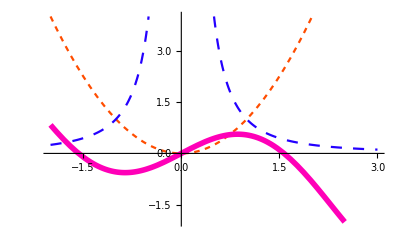

```mathematica
Plot[{x^2,1/x^2,x Cos[x]},{x,-2,3},PlotRange->{-2,4},PlotStyle->{{Dashing[{.01}],Hue[0.05]},{Dashing[{.02}],Hue[0.69]},{Thickness[.01],Hue[0.88]}}]
```

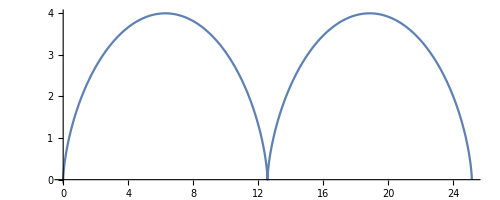

```mathematica
r=2;
ParametricPlot[{r(t-Sin[t]),r(1-Cos[t])},{t,0,4π}]
```

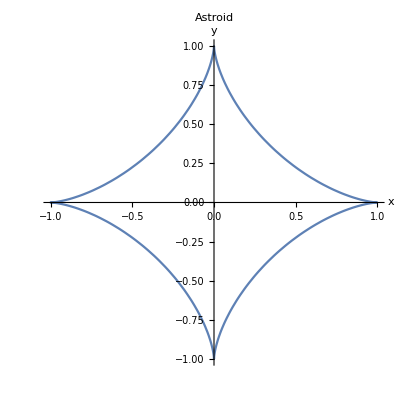

```mathematica
a=1;
ParametricPlot[{a(Cos[t])^3,a(Sin[t])^3},{t,0,2π},AxesLabel->{x,y},PlotLabel->Style[Framed[Astroid],16,Blue,Underlined,Background->Yellow]]
```

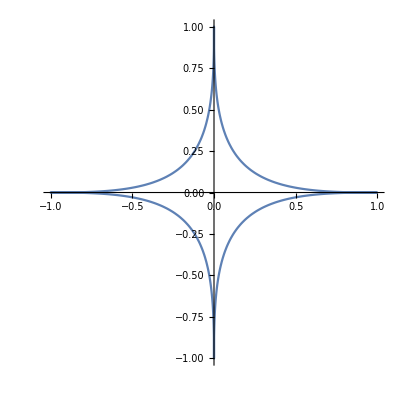

```mathematica
p=2;
ParametricPlot[{(Cos[t])^(2 p+1),(Sin[t])^(2 p+1)},{t,0,2 π}]
```

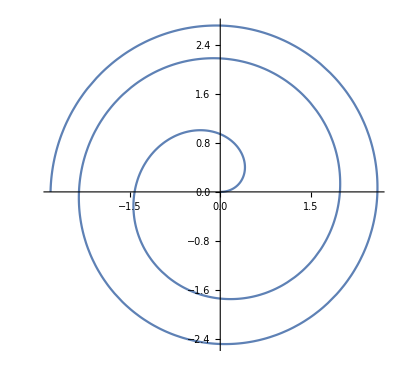

```mathematica
PolarPlot[Log[t+1],{t,0,5 π}]
```

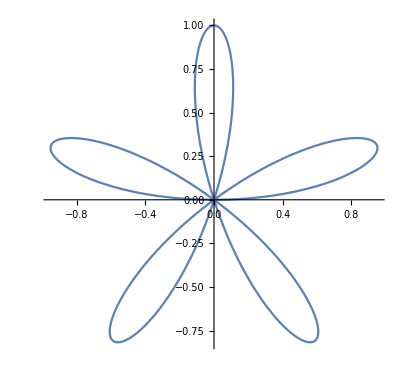

```mathematica
PolarPlot[Sin[5 t],{t,0,Pi}]
```

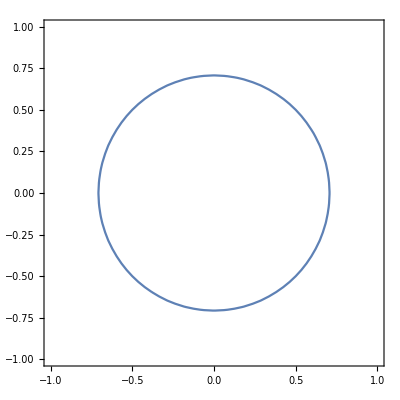

```mathematica
ContourPlot[x^2+y^2==1/2,{x,-1,1},{y,-1,1}]
```

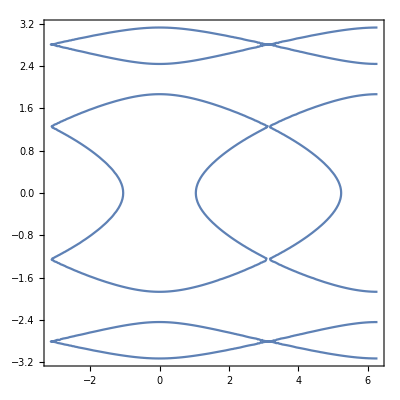

```mathematica
ContourPlot[2 Cos[x]+3 Sin[y^2]-1==0,{x,-Pi,2 Pi},{y,-π,π}]
```

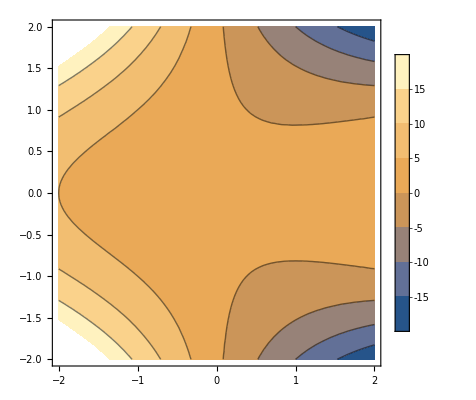

```mathematica
ContourPlot[x^2-3 x y^2+1,{x,-2,2},{y,-2,2},PlotLegends->Automatic]
```

```mathematica
(* Графики, криви и повърхнини в пространството *)
Plot3D[Cos[5 x] y^3-2 x^2 Sin[5 x],{x,0,Pi},{y,0,π}]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x^2+y^2],(2 x y^2-x^3 y)/40},{x,-3,3},{y,-2,2},PlotRange->All]
```

-Graphics3D-

```mathematica
s=1;
r=5;
ParametricPlot3D[{r*Cos[t],r*Sin[t],s*t},{t,0,10 π}]
```

-Graphics3D-

```mathematica
gr1=ParametricPlot3D[{Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]},{u,0,Pi},{v,0,2π}];
gr2=ParametricPlot3D[{1/2 Cos[v],1/2 Sin[v]+1/2,u},{u,-1,1},{v,0,2π}];
Show[{gr1,gr2},PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
graph1=ParametricPlot3D[{u Cos[v],u Sin[v]+1/2,√(1-(u Cos[v])^2-(u Sin[v]+1/2)^2)},{u,0,1/2},{v,0,2π}];
graph2=ParametricPlot3D[{u Cos[v],u Sin[v]+1/2,-√(1-(u Cos[v])^2-(u Sin[v]+1/2)^2)},{u,0,1/2},{v,0,2π}];
Show[{graph1,graph2},PlotRange->Automatic]
```

-Graphics3D-